# ToW Zone Extent

We want to find how far the ToW zone extends for the various experimental geometries. The setup is like this:

-Graphics-

Above is a top down view, below is a view looking through side a

-Graphics-

## Derivation of ToW zone extent

To find d, the extent of the ToW zone, we can use some trig. Pythagorean theorem on the red triangle gives

```mathematica
eq1=a==Sqrt[(2R+2L+2RMT)^2-s^2]
```

a==√((2 L+2 R+2 RMT)^2-s^2)

Then the sine of θ in the blue triangle is

```mathematica
eq2=Sin[θ]==a/d
```

Sin[θ]==a/d

Solve this to find

```mathematica
soln=Solve[{eq1,eq2},d,{a}]//Simplify
```

{{d→√((2 L+2 R+2 RMT-s) (2 L+2 R+2 RMT+s)) Csc[θ]}}

So our solution is

```mathematica
ToWzone=d/.soln[[1]]//FullSimplify
```

√(4 (L+R+RMT)^2-s^2) Csc[θ]

```mathematica
CForm[ToWzone]
```

Sqrt(4*Power(L + R + RMT,2) - Power(s,2))*Csc(θ)

## Testing

We should make sure this function behaves as it should. First, as θ gets close to 0 or π, the ToW zone should become infinitely long

```mathematica
Simplify[Limit[ToWzone,θ->0],Assumptions->{0<L<Infinity,0<R<Infinity,0<s<2L+2R}]
```

∞

```mathematica
Simplify[Limit[ToWzone,θ->Pi],Assumptions->{0<L<Infinity,0<R<Infinity,0<s<2L+2R}]
```

-∞

The situation is somewhat more simple for case where s→0, where the geometry looks like this

-Graphics-

From this we can see that in this geometry

```mathematica
Solve[Sin[θ]==(2L+2R)/d,d]
```

{{d→2 (L+R) Csc[θ]}}

The full solution should match this

```mathematica
Simplify[Limit[ToWzone,s->0],Assumptions->{L>0,R>0,s>0,0<θ<Pi}]
```

2 (L+R) Csc[θ]

```mathematica
Simplify[Limit[ToWzone,s->0]/.θ->Pi/2,Assumptions->{L>0,R>0,s>0}]
```

2 (L+R)

-Graphics-

```mathematica
Sqrt[(2R+2L)^2-s^2]//Simplify
```

√(4 (L+R)^2-s^2)

```mathematica
ToWzone/.θ->Pi/2//FullSimplify
```

√(4 (L+R)^2-s^2)

## Investigation of ToW zone

We can plot the extent of the ToW zone as a function of θ

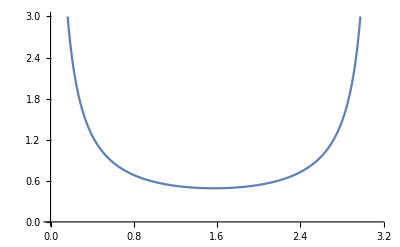

```mathematica
Plot[ToWzone/.{L->.057,R->.5,s->1},{θ,0,Pi},PlotRange->{0,3}]
```

As well as find the values for each of the experimental geometries

```mathematica
TableForm[ToWzone/.{L->.057,R->.5}/.
{{{s->0,θ->30°},{s->0,θ->90°},{s->0,θ->150°}},{{s->.5,θ->30°},{s->.5,θ->90°},{s->.5,θ->150°}},
{{s->1,θ->30°},{s->1,θ->90°},{s->1,θ->150°}}}
,TableHeadings->{{0,.5,1},{"Acute","Normal","Obtuse"}}]
```

| Acute | Normal | Obtuse
0 | 2.228 | 1.114 | 2.228
0.5 | 1.99098 | 0.995488 | 1.99098
1 | 0.981827 | 0.490913 | 0.981827